```mathematica
ClearAll;
ClearAll["`*", Subscript, Derivative];
ClearAll["Global`*",Derivative,Subscript];
β= (-s )(Cosh[r]-ⅇ^(ⅈ θ) Sinh[r]);
NN=1/(√2)(1+Abs[A]^2+ (1-Abs[A]^2)(1-Abs[β]^2 )ⅇ^(-1/2  Abs[β]^2) )^(-1/2);
```

```mathematica
Subscript[Q, 1]= 2 Abs[NN]^2((Conjugate[A]+ A )s/2+1/Sinh[r]^2(Conjugate[A]-A)  Subscript[p, 1]);(*<a>*)
Subscript[X, 1]=1/2 s (Cosh[r]-ⅇ^(ⅈ θ) Sinh[r]);
Subscript[X, 2]=1/2 (-s) (Cosh[r]-ⅇ^(-ⅈ θ) Sinh[r]);
Subscript[p, 1]=Subscript[h, 1]+s/2(Subscript[h, 2]-Subscript[h, 3])-s^2/4 Subscript[h, 4];
Subscript[h, 1]=(  Subscript[X, 2] Subscript[X, 1]^2 Cosh[r](1+3 Sinh[r]^2) + Subscript[X, 2]^2 Subscript[X, 1] ⅇ^(ⅈ θ) Sinh[r](2+3 Sinh[r]^2)+Subscript[X, 2]^3 ⅇ^(2ⅈ θ) Sinh[r]^2 Cosh[r]+Subscript[X, 1]^3 ⅇ^(-ⅈ θ) Sinh[r] Cosh[r]^2+Subscript[X, 2] ⅇ^(ⅈ θ) Sinh[r](1+3 Sinh[r]^2)+3 Subscript[X, 1] Sinh[r]^2 Cosh[r])ⅇ^(-1/2 s^2 Abs[Cosh[r]-ⅇ^(ⅈ θ) Sinh[r]]^2) ;
Subscript[h, 2]= (Subscript[X, 1]^2 ⅇ^(2ⅈθ)Sinh[r]^2+Subscript[X, 1]^2 Cosh[r]^2+(2 Subscript[X, 1] Subscript[X, 2]+1)ⅇ^(ⅈ θ)Sinh[r]Cosh[r])ⅇ^(-1/2 s^2 Abs[Cosh[r]-ⅇ^(ⅈ θ) Sinh[r]]^2);
Subscript[h, 3]=(Subscript[X, 1] Subscript[X, 2] Cosh[2r]+(Subscript[X, 2]^2 ⅇ^(ⅈ θ)+Subscript[X, 1]^2 ⅇ^(-ⅈ θ))Sinh[r]Cosh[r]+Sinh[r]^2)ⅇ^(-1/2 s^2 Abs[Cosh[r]-ⅇ^(ⅈ θ) Sinh[r]]^2);
Subscript[h, 4] = (Subscript[X, 1] Cosh[r]+Subscript[X, 2] ⅇ^(ⅈ θ)Sinh[r])ⅇ^(-1/2 s^2 Abs[Cosh[r]-ⅇ^(ⅈ θ) Sinh[r]]^2);
```

```mathematica
Subscript[Q, 2]=2 Abs[NN]^2((1+ Abs[A]^2 )(3/2 ⅇ^(ⅈ θ) Sinh[2r]+s^2/4)+1/Sinh[r]^2(1-Abs[A]^2)Subscript[p, 2] );(*<a^2>*)
Subscript[p, 2]=Subscript[h, 5]+s/2(Subscript[h, 6]-Subscript[h, 7])-s^2/4 Subscript[h, 8];
Subscript[h, 5]=(  Subscript[X, 2] Subscript[X, 1]^3 Cosh[r]^4+3( Subscript[X, 2]^2 Subscript[X, 1]^2+Subscript[X, 2] Subscript[X, 1] )ⅇ^(ⅈ θ) Cosh[r]^3 Sinh[r]+3(Subscript[X, 2]^3 Subscript[X, 1]+Subscript[X, 2]^2)ⅇ^(2ⅈ θ) Sinh[r]^2 Cosh[r]^2+Subscript[X, 2]^4 ⅇ^(3ⅈ θ) Cosh[r] Sinh[r]^3+Subscript[X, 1]^4 ⅇ^(-ⅈ θ) Sinh[r] Cosh[r]^3+3(Subscript[X, 2] Subscript[X, 1]^3+2 Subscript[X, 1]^2)Sinh[r]^2 Cosh[r]^2+3(Subscript[X, 2]^2 Subscript[X, 1]^2+3 Subscript[X, 2] Subscript[X, 1]+1)ⅇ^(ⅈ θ) Sinh[r]^3 Cosh[r]+(Subscript[X, 2]^3 Subscript[X, 1]+3 Subscript[X, 2]^2)ⅇ^(2ⅈ θ) Sinh[r]^4)ⅇ^(-1/2 s^2 Abs[Cosh[r]-ⅇ^(ⅈ θ) Sinh[r]]^2) ;
Subscript[h, 6]= (Subscript[X, 1]^3 Cosh[r]^3+3(Subscript[X, 2] Subscript[X, 1]^2+Subscript[X, 1])ⅇ^(ⅈ θ)Cosh[r]^2 Sinh[r]+3(Subscript[X, 2]^2 Subscript[X, 1]+Subscript[X, 2])ⅇ^(2ⅈ θ)Cosh[r] Sinh[r]^2+Subscript[X, 2]^3 ⅇ^(3ⅈ θ)Sinh[r]^3)ⅇ^(-1/2 s^2 Abs[Cosh[r]-ⅇ^(ⅈ θ) Sinh[r]]^2); 
Subscript[h, 7]= (  Subscript[X, 2] Subscript[X, 1]^2 Cosh[r](1+3 Sinh[r]^2) + Subscript[X, 2]^2 Subscript[X, 1] ⅇ^(ⅈ θ) Sinh[r](2+3 Sinh[r]^2)+Subscript[X, 2]^3 ⅇ^(2ⅈ θ) Sinh[r]^2 Cosh[r]+Subscript[X, 1]^3 ⅇ^(-ⅈ θ) Sinh[r] Cosh[r]^2+Subscript[X, 2] ⅇ^(ⅈ θ) Sinh[r](1+3 Sinh[r]^2)+3 Subscript[X, 1] Sinh[r]^2 Cosh[r])ⅇ^(-1/2 s^2 Abs[Cosh[r]-ⅇ^(ⅈ θ) Sinh[r]]^2) ;
Subscript[h, 8]=(Subscript[X, 1]^2 ⅇ^(2ⅈθ)Sinh[r]^2+Subscript[X, 1]^2 Cosh[r]^2+(2 Subscript[X, 1] Subscript[X, 2]+1)ⅇ^(ⅈ θ)Sinh[r]Cosh[r])ⅇ^(-1/2 s^2 Abs[Cosh[r]-ⅇ^(ⅈ θ) Sinh[r]]^2);
```

```mathematica
Subscript[Q, 3]=Abs[NN]^2(2(  1+ Abs[A]^2 )(1+3 Sinh[r]^2+s^2/4)+2/Sinh[r]^2(Conjugate[(1-A)](1+A) )Subscript[p, 3]);
Subscript[p, 3] = Subscript[h, 9]+s/2(Subscript[h, 10]-Subscript[h, 11])-s^2/4 Subscript[h, 12];
Subscript[h, 9]=(Subscript[l, 1]+Subscript[l, 2]+Subscript[l, 3]) ⅇ^(-1/2 s^2 Abs[Cosh[r]-ⅇ^(ⅈ θ) Sinh[r]]^2);(* <ξ , -s/2 | a^+a^+aa|s/2,ξ > *)
Subscript[l, 1]=Subscript[X, 2]^2  Subscript[X, 1]^2 Cosh[r]^4 +(2 Subscript[X, 2]^3  Subscript[X, 1] +Subscript[X, 2]^2)ⅇ^(ⅈ θ) Cosh[r]^3 Sinh[r]+Subscript[X, 2]^4 ⅇ^(2ⅈ θ) Sinh[r]^2 Cosh[r]^2;Subscript[l, 2]=(2 Subscript[X, 2]  Subscript[X, 1]^3 +Subscript[X, 1]^2)ⅇ^(-ⅈ θ) Sinh[r] Cosh[r]^3+ (4 Subscript[X, 2]^2  Subscript[X, 1]^2+8 Subscript[X, 2]  Subscript[X, 1]+1)Sinh[r]^2 Cosh[r]^2+(2 Subscript[X, 2]^3  Subscript[X, 1]+5 Subscript[X, 2]^2)ⅇ^(ⅈ θ) Sinh[r]^3 Cosh[r];Subscript[l, 3]=Subscript[X, 1]^4 ⅇ^(-2ⅈ θ)Sinh[r]^2 Cosh[r]^2+(2 Subscript[X, 2]  Subscript[X, 1]^3+5 Subscript[X, 1]^2)ⅇ^(-ⅈ θ)  Sinh[r]^3  Cosh[r]+( Subscript[X, 2]^2  Subscript[X, 1]^2+4 Subscript[X, 2]  Subscript[X, 1] +2 )Sinh[r]^4   ; 
Subscript[h, 10]=(  Subscript[X, 2] Subscript[X, 1]^2 Cosh[r](1+3 Sinh[r]^2) + Subscript[X, 2]^2 Subscript[X, 1] ⅇ^(ⅈ θ) Sinh[r](2+3 Sinh[r]^2)+Subscript[X, 2]^3 ⅇ^(2ⅈ θ) Sinh[r]^2 Cosh[r]+Subscript[X, 1]^3 ⅇ^(-ⅈ θ) Sinh[r] Cosh[r]^2+Subscript[X, 2] ⅇ^(ⅈ θ) Sinh[r](1+3 Sinh[r]^2)+3 Subscript[X, 1] Sinh[r]^2 Cosh[r])ⅇ^(-1/2 s^2 Abs[Cosh[r]-ⅇ^(ⅈ θ) Sinh[r]]^2) ;
Subscript[h, 11]= (  Subscript[X, 2] Subscript[X, 1]^2 Cosh[r](1+3 Sinh[r]^2) + Subscript[X, 2]^2 Subscript[X, 1] ⅇ^(ⅈ θ) Sinh[r](2+3 Sinh[r]^2)+Subscript[X, 2]^3 ⅇ^(2ⅈ θ) Sinh[r]^2 Cosh[r]+Subscript[X, 1]^3 ⅇ^(-ⅈ θ) Sinh[r] Cosh[r]^2+Subscript[X, 2] ⅇ^(ⅈ θ) Sinh[r](1+3 Sinh[r]^2)+3 Subscript[X, 1] Sinh[r]^2 Cosh[r])ⅇ^(-1/2 s^2 Abs[Cosh[r]-ⅇ^(ⅈ θ) Sinh[r]]^2);
Subscript[h, 12]=(Subscript[X, 1] Subscript[X, 2] Cosh[2r]+(Subscript[X, 2]^2 ⅇ^(ⅈ θ)+Subscript[X, 1]^2 ⅇ^(-ⅈ θ))Sinh[r]Cosh[r]+Sinh[r]^2)ⅇ^(-1/2 s^2 Abs[Cosh[r]-ⅇ^(ⅈ θ) Sinh[r]]^2) ;
```

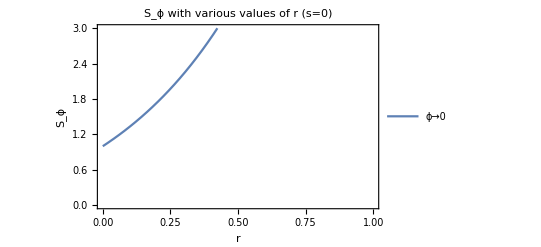

```mathematica
SQ=Subscript[W, 2]-( Subscript[W, 1])^2-1/2(*Squeezing parameter Subscript[S, θ] = <Subscript[X, θ]^2>-<Subscript[X, θ]>^2-1/2 *);
Subscript[W, 1]= √2 Re[Subscript[Q, 1] ⅇ^(-ⅈ ϕ)];(*where Subscript[X, 1] = <Subscript[X, θ]> =1/(√2) (<a>ⅇ^(-ⅈ θ)+<a^+>ⅇ^(ⅈ θ))*)
Subscript[W, 2]=1/2(2Re[ Subscript[Q, 2] ⅇ^(-2ⅈ ϕ)]+2 Subscript[Q, 3]+1);(*where Subscript[X, 2] = <Subscript[X, θ]^2> =1/2(2Re[<a^2>ⅇ^(-2ⅈ θ)]+2<a^+a>+1)=1/2(2Re[Subscript[Q, 2]*ⅇ^(-2ⅈ θ)]+2 Subscript[Q, 3]+1) *)
A=ⅇ^(ⅈ δ) Tan[α/2];
range={0,π/12,π/6,π/4,π/3,(5π)/12,π/2};
Plot[Evaluate[SQ/.{s->0,ϕ->range,δ->π,θ->π ,α->(9π)/8}],{r,0,1},PlotRange->{0,3},PlotLegends->(StringForm["ϕ→``",#]&/@range),PlotLabel->HoldForm[Subscript[S, ϕ] with various values of r (s=0)],AxesLabel->{HoldForm[r],HoldForm[Subscript[S, ϕ]]},PlotRange->Full,Frame->True]
```